```mathematica
(*pixel diff data*)
directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
mlfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxunfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
mlunfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manual/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
manual=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
manfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxunfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
manunfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxunfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
funfilt=Import[#,"CSV"]&/@fileNames;

directory="/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxfilt data/pixel_diff/";
fileNames=Table[directory<>"pix_data_"<>IntegerString[i]<>".csv",{i,1,20}];
filfilt=Import[#,"CSV"]&/@fileNames;

(*mlfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxfilt data/pixel_diff/"];
mlunfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/mlxunfilt data/pixel_diff/"];
manual=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manual/pixel_diff/"];
manfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxfilt data/pixel_diff/"];
manunfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/manxunfilt data/pixel_diff/"];
funfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxunfilt data/pixel_diff/"];
filfilt=FileNames["*.csv", "/Users/ashna/Desktop/6BBB0371 project data/mathematica data/filtxfilt data/pixel_diff/"];*)
```

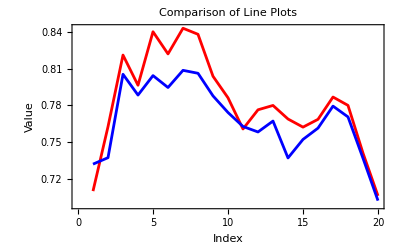

```mathematica
y=ListLinePlot[Flatten[mlfilt],PlotStyle->Red,Frame->True,FrameLabel->{"x","y"}];
z=ListLinePlot[Flatten[mlunfilt],PlotStyle->Blue,Frame->True,FrameLabel->{"x","y"}];

(*K ML x A filt vs K ML x A unfilt*)
Show[y,z,Frame->True,FrameLabel->{"Index","Value"},PlotLabel->"Comparison of Line Plots"]
```

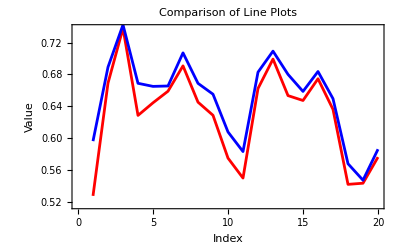

```mathematica
(*manual x ML (filt and unfilt)*)
y=ListLinePlot[Flatten[manfilt],PlotStyle->Red,Frame->True,FrameLabel->{"x","y"}];
z=ListLinePlot[Flatten[manunfilt],PlotStyle->Blue,Frame->True,FrameLabel->{"x","y"}];
Show[y,z,Frame->True,FrameLabel->{"Index","Value"},PlotLabel->"Comparison of Line Plots"]
```

{{{0.516861}},{{0.651897}},{{0.653048}},{{0.492815}},{{0.657379}},{{0.661901}},{{0.696264}},{{0.666014}},{{0.607374}},{{0.613254}},{{0.593747}},{{0.660632}},{{0.695824}},{{0.671487}},{{0.649749}},{{0.694081}},{{0.680748}},{{0.630984}},{{0.62186}},{{0.662162}}}

{{{0.673812}},{{0.826612}},{{0.820438}},{{0.640385}},{{0.829268}},{{0.830831}},{{0.844918}},{{0.819109}},{{0.77303}},{{0.770867}},{{0.754504}},{{0.818848}},{{0.85355}},{{0.831743}},{{0.81462}},{{0.845628}},{{0.829793}},{{0.783645}},{{0.770676}},{{0.810632}}}

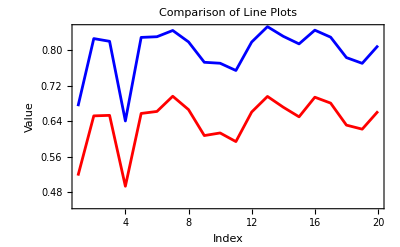

```mathematica
(*filtxunfilt vs filtxfilt*)
funfilt
filfilt

y=ListLinePlot[Flatten[funfilt],PlotStyle->Red,Frame->True,FrameLabel->{"x","y"}];
z=ListLinePlot[Flatten[filfilt],PlotStyle->Blue,Frame->True,FrameLabel->{"x","y"}];
Show[y,z,Frame->True,FrameLabel->{"Index","Value"},PlotLabel->"Comparison of Line Plots", PlotRange->{0.45, 0.85}]
```

```mathematica
a=Flatten[mlunfilt];
b=Flatten[mlfilt];
c=Flatten[manual];
d=Flatten[manfilt];
e=Flatten[manunfilt];
f=Flatten[funfilt];
g=Flatten[filfilt];
```

```mathematica
descriptiveStats={{Mean[#],Median[#],StandardDeviation[#],Min[#],Max[#]}&/@{a,b,c,d,e,f,g}};

descriptiveStats[[1]]
```

{{0.768324,0.768875,0.0295617,0.701839,0.808817},{0.78276,0.780016,0.0388171,0.705754,0.843384},{0.74157,0.740613,0.0483321,0.64713,0.820923},{0.629681,0.644913,0.0583775,0.527856,0.737974},{0.650835,0.665334,0.0520998,0.547493,0.742283},{0.638904,0.655213,0.0541794,0.492815,0.696264},{0.797145,0.818979,0.0556556,0.640385,0.85355}}

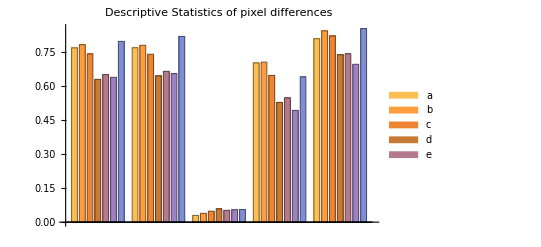

```mathematica
BarChart[Transpose[descriptiveStats[[1]]],ChartLegends->{"a","b","c","d","e"},PlotLabel->"Descriptive Statistics of pixel differences"]
```

```mathematica
(*bland-altmann test*)
Clear[BlandAltmanPlot]

BlandAltmanPlot[meanList_,diffList_,datasetLabel_]:=ListPlot[Transpose[{meanList,diffList}],PlotMarkers->{Automatic,8},FrameLabel->{"Mean","Difference"},PlotLabel->{"Bland-Altman Plot for "<>datasetLabel},ImageSize->400]

(*Debugging code*)
meanListA=Mean[a]
diffListA=Differences[a]

meanListB=Mean[b];
diffListB=Differences[b];

meanListC=Mean[c];
diffListC=Differences[c];

meanListD=Mean[d];
diffListD=Differences[d];

meanListE=Mean[e];
diffListE=Differences[e];

meanListF=Mean[f];
diffListF=Differences[f];

meanListG=Mean[g];
diffListG=Differences[g];

(*Combine mean and difference lists for all datasets*)
combinedMeanList={meanListA,meanListB,meanListC,meanListD,meanListE,meanListF,meanListG};
combinedDiffList={diffListA,diffListB,diffListC,diffListD,diffListE,diffListF,diffListG};

(*Plot Bland-Altman*)
BlandAltmanPlot[combinedMeanList,combinedDiffList,"Dataset A-G"]
```

0.768324

{0.00529632,0.0684871,-0.0170683,0.0159839,-0.00978209,0.0140952,-0.0024145,-0.0185631,-0.0136332,-0.011483,-0.0045044,0.00895816,-0.0302904,0.0152036,0.00928975,0.0180631,-0.00887115,-0.0339378,-0.034795}

-Graphics-

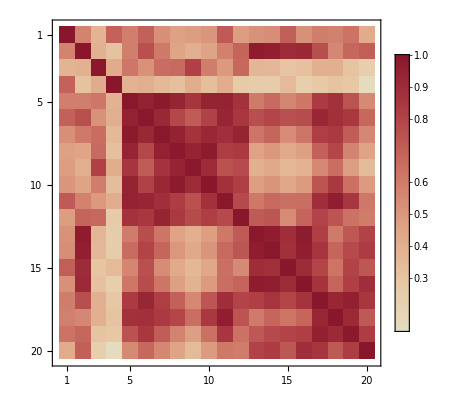

```mathematica
correlationMatrix=Correlation[{a,b,c,d,e,f,g}];

(*Visualize the correlation matrix as a heatmap*)
MatrixPlot[correlationMatrix,ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

0.949769

0.968733

0.988629

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

{{{0.516861}},{{0.651897}},{{0.653048}},{{0.492815}},{{0.657379}},{{0.661901}},{{0.696264}},{{0.666014}},{{0.607374}},{{0.613254}},{{0.593747}},{{0.660632}},{{0.695824}},{{0.671487}},{{0.649749}},{{0.694081}},{{0.680748}},{{0.630984}},{{0.62186}},{{0.662162}}}

-Graphics-

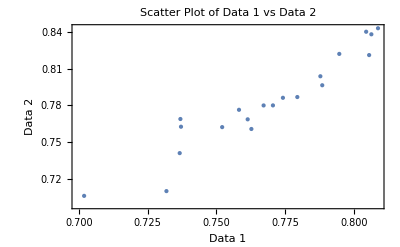

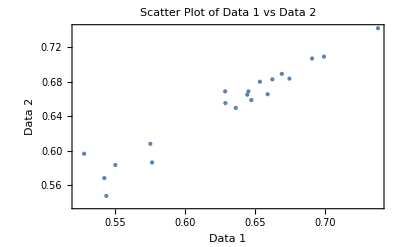

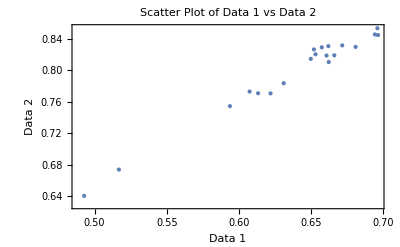

```mathematica
pearsonCoefficient=Correlation[a,b]
pearsonCoefficient=Correlation[d,e]
pearsonCoefficient=Correlation[f,g]

(*Remove duplicates*)

lm=LinearModelFit[Transpose[{funfilt,filfilt}],x,x];
funfilt
(*Plot the data and the fit line*)
plot=ListPlot[Transpose[{funfilt,filfilt}],PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"Data 1","Data 2"},PlotLabel->"Scatter Plot of Data 1 vs Data 2"];

Show[plot,Plot[lm[x],{x,Min[f],Max[f]},PlotStyle->Red]]

(*Visualize the relationship between the datasets*)
ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"Data 1","Data 2"},PlotLabel->"Scatter Plot of Data 1 vs Data 2"]

ListPlot[Transpose[{d,e}],PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"Data 1","Data 2"},PlotLabel->"Scatter Plot of Data 1 vs Data 2"]

ListPlot[Transpose[{f,g}],PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"Data 1","Data 2"},PlotLabel->"Scatter Plot of Data 1 vs Data 2"]
```

```mathematica
(*ANCOVA tests*)
(*Per dataset ancova*)
(*Define the covariate variable*)covariate={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26};

(*Define the datasets*)
datasets={a,b};

(*Perform ANCOVA for each dataset*)
ANCOVAResults=Table[ANCOVA[Transpose[{covariate,datasets[[i]]}]],{i,1,Length[datasets]}];

(*Display ANCOVA results*)
ANCOVAResults
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«16»},{0.731805,0.737101,0.805588,0.78852,0.804504,0.794722,0.808817,0.806403,0.78784,0.774206,«10»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«16»},{0.70966,0.762529,0.821348,0.796568,0.840508,0.822312,0.843384,0.838407,0.803949,0.786274,«10»}} cannot be transposed.

{ANCOVA[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26},{0.731805,0.737101,0.805588,0.78852,0.804504,0.794722,0.808817,0.806403,0.78784,0.774206,0.762723,0.758219,0.767177,0.736887,0.75209,0.76138,0.779443,0.770572,0.736634,0.701839}}]],ANCOVA[Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26},{0.70966,0.762529,0.821348,0.796568,0.840508,0.822312,0.843384,0.838407,0.803949,0.786274,0.760669,0.77642,0.779994,0.768859,0.762195,0.768592,0.786895,0.780037,0.74085,0.705754}}]]}

```mathematica
(*paired dataset ancova*)
(*Perform ANCOVA for pairs of datasets*)ANCOVAResultsPairs=Table[ANCOVA[Transpose[{covariate,datasets[[i]]}],Transpose[{covariate,datasets[[j]]}]],{i,1,Length[datasets]},{j,i+1,Length[datasets]}];

(*Display ANCOVA results for each pair*)
ANCOVAResultsPairs;
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«16»},{0.731805,0.737101,0.805588,0.78852,0.804504,0.794722,0.808817,0.806403,0.78784,0.774206,«10»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«16»},{0.70966,0.762529,0.821348,0.796568,0.840508,0.822312,0.843384,0.838407,0.803949,0.786274,«10»}} cannot be transposed.

```mathematica
tTest=TTest[{a,b}]
tTest=TTest[{d,e}]
tTest=TTest[{f,g}]
```

0.193668

0.234104

TTest::nortst: At least one of the p-values in {0.00768748,0.00288151}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

4.24963×10^-11

```mathematica
chiSquareTest=PearsonChiSquareTest[a]
chiSquareTest=PearsonChiSquareTest[b]
chiSquareTest=PearsonChiSquareTest[c]
chiSquareTest=PearsonChiSquareTest[d]
chiSquareTest=PearsonChiSquareTest[e]
chiSquareTest=PearsonChiSquareTest[f]
chiSquareTest=PearsonChiSquareTest[g]
```

0.206742

0.433749

0.541232

0.267385

0.158598

0.0214838

0.00184836

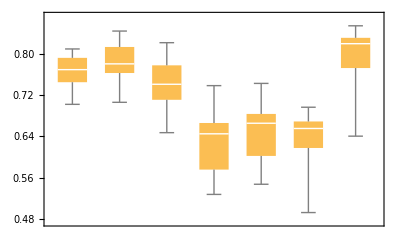

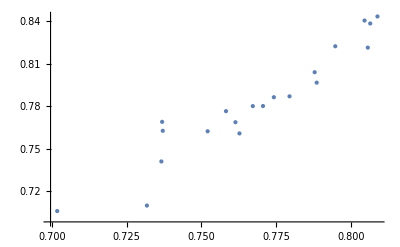

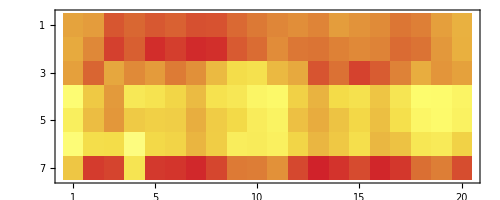

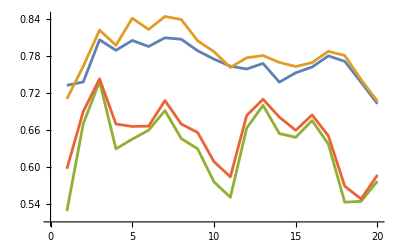

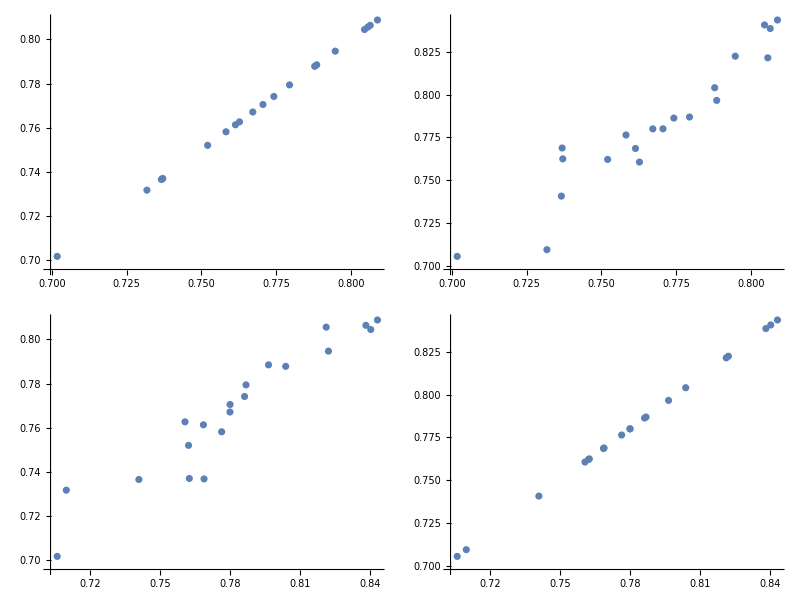

```mathematica
(*visual stats*)

Histogram[b];
Histogram[c];

BoxWhiskerChart[{a,b,c,d,e,f,g}]

ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Medium]]

MatrixPlot[{a,b,c,d,e,f,g},ColorFunction->"TemperatureMap"]

BarChart[{a,b,c,d,e,f,g}];

ListLinePlot[{a,b,d,e}]

Grid[Table[ListPlot[Transpose[{a,b}[[{i,j}]]]],{i,1,2},{j,1,2}]]
```

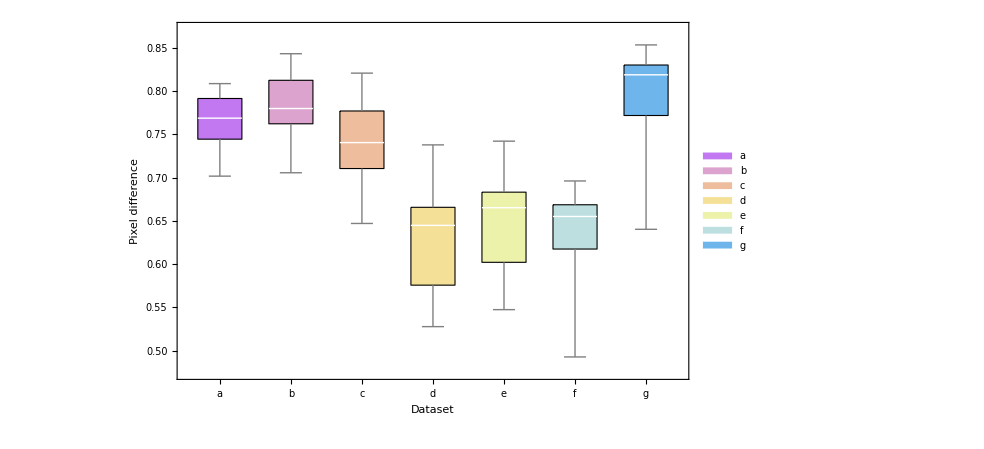

```mathematica
BoxWhiskerChart[{a,b,c,d,e,f,g},ChartStyle->{EdgeForm[Black],"Pastel"},ChartLegends->{"a","b","c","d","e","f","g"},FrameLabel->{"Dataset", "Pixel difference"}, ChartLabels->{"a","b","c","d","e","f","g"}, Background->White, LabelStyle->Medium]
```

```mathematica
ShapiroWilkTest[d]
```

0.201587

```mathematica
datasets={a,b,c,d,e,f,g};

anovaResult=ANOVA[datasets];

TableForm[anovaResult["ANOVATable"]]
```

ANOVA[{{0.731805,0.737101,0.805588,0.78852,0.804504,0.794722,0.808817,0.806403,0.78784,0.774206,0.762723,0.758219,0.767177,0.736887,0.75209,0.76138,0.779443,0.770572,0.736634,0.701839},{0.70966,0.762529,0.821348,0.796568,0.840508,0.822312,0.843384,0.838407,0.803949,0.786274,0.760669,0.77642,0.779994,0.768859,0.762195,0.768592,0.786895,0.780037,0.74085,0.705754},{0.734655,0.789603,0.715718,0.761491,0.737905,0.772409,0.755136,0.693273,0.65276,0.64713,0.693421,0.712578,0.806094,0.781927,0.820923,0.801206,0.768716,0.708679,0.743321,0.734464},{0.527856,0.669207,0.737974,0.628705,0.644515,0.65905,0.690816,0.645311,0.628858,0.575181,0.55017,0.662405,0.69931,0.653536,0.647406,0.674645,0.636268,0.542278,0.543703,0.576431},{0.596469,0.68926,0.742283,0.668963,0.665086,0.665583,0.707096,0.668917,0.655281,0.607969,0.583373,0.682894,0.709264,0.680136,0.658781,0.683734,0.64968,0.568152,0.547493,0.586294},{0.516861,0.651897,0.653048,0.492815,0.657379,0.661901,0.696264,0.666014,0.607374,0.613254,0.593747,0.660632,0.695824,0.671487,0.649749,0.694081,0.680748,0.630984,0.62186,0.662162},{0.673812,0.826612,0.820438,0.640385,0.829268,0.830831,0.844918,0.819109,0.77303,0.770867,0.754504,0.818848,0.85355,0.831743,0.81462,0.845628,0.829793,0.783645,0.770676,0.810632}}][ANOVATable]